```mathematica
(*Ladder operators and Phi/Pi in HO basis*)
LadderOps[ns_]:=Module[{a,ad},a=ConstantArray[0,{ns,ns}];
Do[a[[n,n+1]]=Sqrt[n],{n,1,ns-1}];
ad=Transpose[a];
{a,ad}];

PhiPiHO[ns_,omega_]:=Module[{a,ad,phi,pi},{a,ad}=LadderOps[ns];
phi=(a+ad)/Sqrt[2 omega];
pi=I Sqrt[omega/2] (ad-a);
phi=Chop[N[phi,30]];
pi=Chop[N[pi,30]];
{phi,pi}];

InteractionPhi4[phi_,lambda_]:=Chop[N[(lambda/24) MatrixPower[phi,4],30]];

(*Split low-energy P-space and high-energy Q-space*)

PQSplitBySizes[nP_,nFull_]:={
Range[1,nP],(*P=low-energy kept states*)
Range[nP+1,nFull]     (*Q=high-energy states*)};

(*HTE energy through O(V^3)*)

EffectiveEnergyHTE[nP_,nFull_,omega_,lambda_,order_:3]:=Module[{phi,pi,H0,energies,V,f=1,i=1,E0,h1,h2,h3,P,Q},(*Build full HO basis of size nFull*){phi,pi}=PhiPiHO[nFull,omega];
H0=Chop[N[1/2 (pi.pi+phi.phi),30]];
energies=Diagonal[H0];
V=InteractionPhi4[phi,lambda];
{P,Q}=PQSplitBySizes[nP,nFull];
E0=energies[[1]];
(*H1 term*)
h1=V[[f,f]];
(*H2 term:sum over Q*)
h2=Sum[V[[f,α]] V[[α,f]]/(E0-energies[[α]]),{α,Q}];
h2=Chop[N[h2,20]];(*gets rid of small imaginary parts*)
(*H3 term:double sum over Q*)
h3=Sum[V[[f,α]] V[[α,β]] V[[β,f]]/((E0-energies[[α]]) (E0-energies[[β]])),{α,Q},{β,Q}];
h3=Chop[N[h3,20]];
(*Assemble energy*)
Chop[N[E0+h1+h2+h3,20]]];

(*Precision function*)

FindPrecisionHTE[nP_,nFull_,omega_,lambda_,E0ref_]:=Module[
{eHTE},eHTE=EffectiveEnergyHTE[nP,nFull,omega,lambda,3];
100 Abs[(eHTE-E0ref)/E0ref]];
```

74.4708

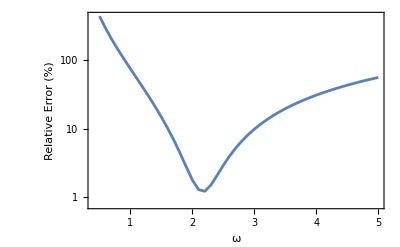

```mathematica
nP=8;       (*kept space size*)
nFull=64;      (*full basis size for Q sums*)
omega=1.0;
lambda=32;
E0ref=0.85974269044550901935596;

FindPrecisionHTE[nP,nFull,omega,lambda,E0ref]

omegaList=Range[0.5,5,0.1];

resultsHTE=Table[{ω,FindPrecisionHTE[nP,nFull,ω,lambda,E0ref]},{ω,omegaList}];

ListLogPlot[resultsHTE,Frame->True,Joined->True,FrameLabel->{"ω","Relative Error (%)"},PlotRange->All]
```

```mathematica
(*------------------------HO BASIS----------------------------*)
LadderOps[ns_]:=Module[
{a,ad},a=ConstantArray[0,{ns,ns}];
Do[a[[n,n+1]]=Sqrt[n],{n,1,ns-1}];
ad=Transpose[a];
{a,ad}];

PhiPiHO[ns_,omega_]:=Module[{a,ad,phi,pi},{a,ad}=LadderOps[ns];
phi=(a+ad)/Sqrt[2 omega];
pi=I Sqrt[omega/2] (ad-a);
{Chop[N[phi,30]],Chop[N[pi,30]]}];

InteractionPhi4[phi_,lambda_]:=Chop[N[(lambda/24) MatrixPower[phi,4],30]];

(*--------------HTE MATRIX (H1+H2+H3)--------------------*)
HTEEffectiveMatrix[nP_,nFull_,omega_,lambda_]:=Module[{phi,pi,H0,evals,evecs,Vraw,V,energies,E0,H1,H2,H3,P,Q,f,i,a,b,termQQ,termMixed},(*Build HO operators in the "truncated" nFull basis*)
{phi,pi}=PhiPiHO[nFull,omega];
(*Free Hamiltonian H0 in the chosen truncated basis*)
H0=Chop[N[1/2 (pi.pi+phi.phi),40]];
(*Diagonalize H0 to obtain eigenvalues/eigenvectors*)
{evals,evecs}=Eigensystem[H0];
(*Sort ascending (Eigensystem may already be sorted,but enforce it)*)
{evals,evecs}=Transpose@SortBy[Transpose[{evals,evecs}],First];
energies=evals;(*energies[[k]]=E_k*)
E0 = energies[[1]];
(*Transform interaction into H0 eigenbasis*)
Vraw=InteractionPhi4[phi,lambda];
V=ConjugateTranspose[evecs].Vraw.evecs;
V=Chop[N[V,40]];(*numeric*)
(*P and Q index sets*)
P=Range[1,nP];Q=Range[nP+1,nFull];(*allocate matrices*)
H1=ConstantArray[0,{nP,nP}];
H2=ConstantArray[0,{nP,nP}];
H3=ConstantArray[0,{nP,nP}];(*compute matrix elements for f,i in P*)
Do[Do[f=ff;i=ii;
(*H1*)
H1[[f,i]]=V[[f,i]];
(*H2*)
H2[[f,i]]=If[Length[Q]>0,Sum[V[[f,a]] V[[a,i]]/(energies[[f]]-energies[[a]]),{a,Q}],0];H2[[f,i]]=Chop[N[H2[[f,i]],30]];
(*H3*)
termQQ=If[Length[Q]>0,Sum[V[[f,a]] V[[a,b]] V[[b,i]]/((energies[[f]]-energies[[a]]) (energies[[f]]-energies[[b]])),{a,Q},{b,Q}],0];termMixed=If[Length[Q]>0,Sum[V[[f,a]] V[[a,b]] V[[b,i]]/((energies[[a]]-energies[[b]]) (energies[[f]]-energies[[b]])),{a,P},{b,Q}],0];H3[[f,i]]=Chop[N[termQQ-termMixed,30]];,{ii,1,nP}],{ff,1,nP}];Chop[N[E0+H1+H2+H3,30]]];


(*-------------------DIGITISATION----------------------------*)
DigitiseHamiltonian[Heff_,nQ_]:=Module[{dim=2^nQ},ArrayPad[Heff,{{0,dim-Length[Heff]},{0,dim-Length[Heff]}}]]

(*----------------PRECISION METRIC---------------------------*)
DigitisedPrecision[nQ_,nFull_,omega_,lambda_,E0ref_]:=Module[{nP,Heff,Hq,E0},nP=2^nQ;
Heff=HTEEffectiveMatrix[nP,nFull,omega,lambda];
Hq=DigitiseHamiltonian[Heff,nQ];
E0=Min[Eigenvalues[Hq]];
100 Abs[(E0-E0ref)/E0ref]];

(*----------------PLOTTING ERROR VS omega-------------------------*)DigitisedSweep[nQList_,omegaList_,lambda_,nFull_,E0ref_]:=Association[Table[nQ->Table[{ω,DigitisedPrecision[nQ,nFull,ω,lambda,E0ref]},{ω,omegaList}],{nQ,nQList}]];

PlotDigitisedResults[data_,nQList_]:=Module[{curves,colors,legendLabels},colors=ColorData["Rainbow"]/@Subdivide[0,1,Length[nQList]-1];
legendLabels=Table["nQ = "<>ToString[nQList[[i]]],{i,Length[nQList]}];
curves=Table[ListLogPlot[data[nQList[[i]]],Joined->True,PlotStyle->{colors[[i]],Thick},PlotLegends->None],{i,Length[nQList]}];
Show[curves,Frame->True,FrameLabel->{"ω","Error (%)"},PlotRange->All,PlotLabel->"Digitised HTE Error vs ω",PlotLegends->Placed[LineLegend[colors,legendLabels,LegendMarkerSize->20],Below]]]
```

Min::nord: Invalid comparison with {3.75139×10^6+0. ⅈ,321112.+0. ⅈ,-611.104+29272. ⅈ,-611.104-29272. ⅈ,7985.45+0. ⅈ,-239.064+0. ⅈ,-9.64817+0. ⅈ,2.15626+0. ⅈ} attempted.

Min::nord: Invalid comparison with {-4793.31+0. ⅈ,-724.341+0. ⅈ,152.148+0. ⅈ,-102.784+0. ⅈ,-11.7484+0. ⅈ,3.48125+0. ⅈ,0.525151+0.274194 ⅈ,0.525151-0.274194 ⅈ} attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

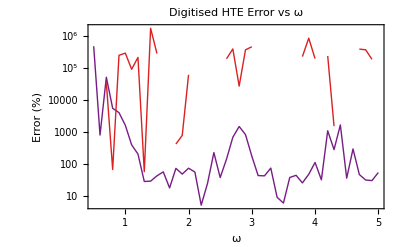

```mathematica
lambda=32;
E0ref=0.85974269044550901935596;

nQList={2,3};        (*qubit counts*)
nFull=80;                (*large HO basis for accurate Q sums*)
omegaList=Range[0.5,5,0.1];

digitisedResults=DigitisedSweep[nQList,omegaList,lambda,nFull,E0ref];

PlotDigitisedResults[digitisedResults,nQList]
```